```mathematica
EmbedGraph5Plantri8[assoc_,key_]:=Block[{val=assoc[key], sets, reference={12,13,7,15,17}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[8]]],14];
g=EdgeDelete[ g,{7<->13,13<->12,12<->17,17<->15,15<->7}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
GraphPower
```

```mathematica
Graph5Plantri8[assoc_,key_]:=Block[{val=assoc[key], sets, reference={12,13,7,15,17}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[8]]],14];
g=EdgeDelete[ g,{7<->13,13<->12,12<->17,17<->15,15<->7}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

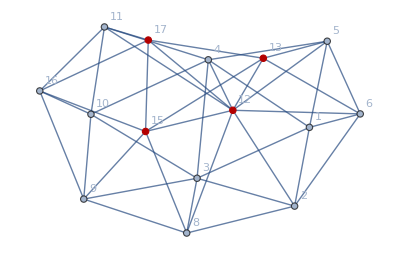

```mathematica
g=Graph[EmbedGraph5Plantri8[allGraphs,quad1Key],GraphHighlight->{12,13,7,15,17}, VertexLabels->"Name"]
```

```mathematica
gge=Map[#[[1]]+100<->#[[2]]+100&,EdgeList[g]]
```

{101<->102,101<->103,101<->104,101<->105,101<->106,102<->106,102<->108,102<->103,103<->108,103<->109,103<->110,103<->104,104<->110,104<->111,104<->105,105<->113,105<->106,106<->113,108<->115,108<->109,109<->115,109<->116,109<->110,110<->116,110<->111,111<->116,111<->117,115<->116,116<->117,112<->102,112<->104,112<->105,112<->106,112<->108,112<->111,112<->113,112<->115,112<->117,113<->115,113<->117,115<->117}

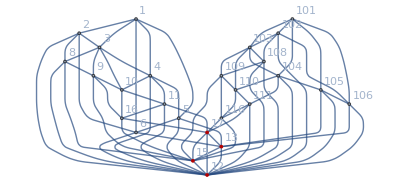

```mathematica
g2=Graph[VertexContract[VertexContract[VertexContract[VertexContract[Graph[Join[EdgeList[g],gge]],{17,117}],{13,113}],{15,115}],{12,112}],VertexLabels->"Name",GraphHighlight->{12,13,7,15,17},GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
EdgeList[g]//Sort
```

{1<->2,1<->3,1<->4,1<->5,1<->6,2<->3,2<->6,2<->8,3<->4,3<->8,3<->9,3<->10,4<->5,4<->10,4<->11,5<->6,5<->13,6<->13,8<->9,8<->15,9<->10,9<->15,9<->16,10<->11,10<->16,11<->16,11<->17,12<->2,12<->4,12<->5,12<->6,12<->8,12<->11,12<->13,12<->15,12<->17,13<->15,13<->17,15<->16,15<->17,16<->17}

```mathematica
VertexCount[g2]
```

26

```mathematica
chromg=ChromaticPolynomial[g,x]
```

8718090 x-38833829 x^2+78592124 x^3-96778380 x^4+81630015 x^5-50178112 x^6+23280741 x^7-8307623 x^8+2296021 x^9-489699 x^10+79390 x^11-9488 x^12+790 x^13-41 x^14+x^15

```mathematica
(chromg*chromg)/ChromaticPolynomial[CompleteGraph[4],x]//Simplify//Expand
```

-12667515541350 x+89628493596395 x^2-302749028773186 x^3+651805611414871 x^4-1006767219601504 x^5+1189823575087719 x^6-1119947122491732 x^7+862522807561504 x^8-553858026947862 x^9+300565855359404 x^10-139179163001414 x^11+55360151888101 x^12-18995770665588 x^13+5634977666016 x^14-1445435064780 x^15+320061064341 x^16-60947727558 x^17+9920046250 x^18-1367712764 x^19+157712930 x^20-14939168 x^21+1132806 x^22-66150 x^23+2794 x^24-76 x^25+x^26

```mathematica
Factor[-6+11 x-6 x^2+x^3]
```

(-3+x) (-2+x) (-1+x)

```mathematica
PlanarGraphQ[g2]
```

False

```mathematica
GraphAutomorphismGroup[g2]
```

PermutationGroup[{Cycles[{{1,12},{2,13},{3,14},{4,15},{5,16},{6,17},{7,18},{8,19},{9,20},{10,21},{11,22}}]}]

```mathematica
GraphAutomorphismGroup[g]
```

PermutationGroup[{}]

```mathematica
PlanarGraphQ[g2]
```

False

```mathematica
VertexCount[g2]
```

26

```mathematica
polg2=ChromaticPolynomial[g2,x]
```

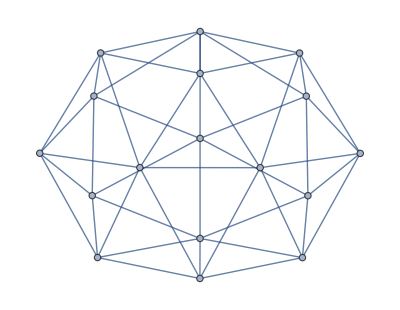

```mathematica
ggg=Graph[plantri[[8]]]
```

```mathematica
Table[v->VertexDegree[ggg,v],{v,{14,12,13,7,15,17}}]
```

{14→5,12→6,13→5,7→6,15→6,17→5}

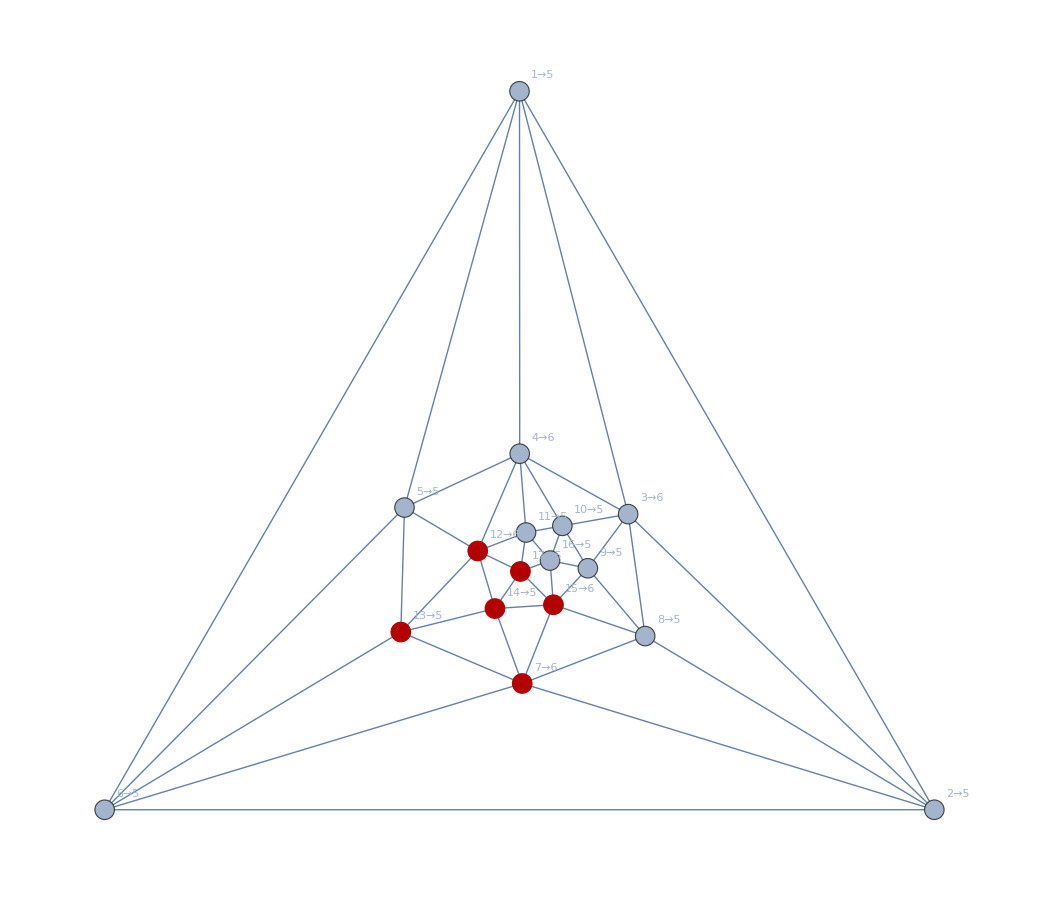

```mathematica
Graph[ggg,VertexLabels->Table[v->{v->VertexDegree[ggg,v]},{v,VertexList[ggg]}],GraphLayout->"TutteEmbedding",GraphHighlight->{14,12,13,7,15,17}]
```